```mathematica
ClearAll[Evaluate[Context[]<>"*"]]
```

```mathematica
Needs["Spline`"];Needs["SubSpaces`"]
```

find all x,y for which the pythagorean mean of the first eigenvalues of the master and submatrix are 1

```mathematica
Clear[x,y,s1,s2,esystems];
H={{0,0,0},{x,y,0},{1,0,0}};
```

```mathematica
Clear[x,y,s1,s2,esystems];
esystems=Eigensystem[#]&/@ListSubSpaces[pascalMatrix[3].H2[pascalMatrix[3],{{1,0,0},{0,1,0},{0,0,1}},{0,0},{x,y},{1,0}]]
s1=esystems[[1]][[1]][[3]]
s2=esystems[[2]][[1]][[1]]
Sqrt[s1^2+s2^2]==1
```

{{{0,0,4 y},{{0,0,1},{0,0,0},{0,-1,1}}},{{-1+4 x,-4 y},{{-(-1+4 x+4 y)/(2 (-1+2 x)),1},{0,1}}}}

4 y

-1+4 x

√((-1+4 x)^2+16 y^2)==1

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→-(√(x-2 x^2))/(√2)},{y→(√(x-2 x^2))/(√2)}}

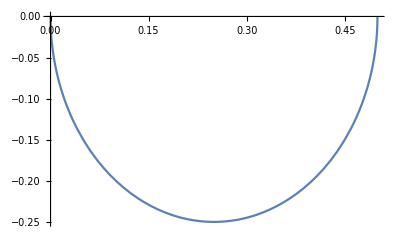

```mathematica
Clear[x,y,s1,s2,esystems];
sol=Solve[esystems=Eigenvalues[#]&/@ListSubSpaces[pascalMatrix[3].H2[pascalMatrix[3],{{1,0,0},{0,1,0},{0,0,1}},{0,0},{x,y},{1,0}]];
s1=esystems[[1]][[3]];
s2=esystems[[2]][[1]];
Sqrt[s1^2+s2^2]==1,{x,y}]
Plot[sol[[1]][[1]][[2]],{x,0,0.5}]
```

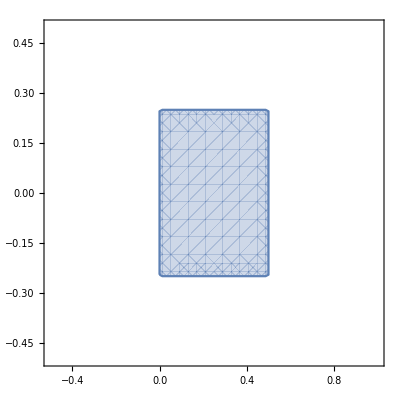

```mathematica
Clear[x,y,s1,s2,esystems];
RegionPlot[esystems=Eigenvalues[#]&/@ListSubSpaces[pascalMatrix[3].H2[pascalMatrix[3],{{1,0,0},{0,1,0},{0,0,1}},{0,0},{x,y},{1,0}]];
s1=esystems[[1]][[3]];
s2=esystems[[2]][[1]];
Sqrt[s1^2+s2^2]<=1,{x,-0.5,1.0},{y,-0.5,0.5}]
```